# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["/Users/pcs/Desktop/Entropy/EMMY r ratios Ising/QMB.wl"];
```

```mathematica
LaunchKernels[10]
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

# <r> open

```mathematica
J=1;
glist=Table[10^i,{i,-5,1.3,0.1}];
newglist=Partition[glist,4];
hlist=Table[10^i,{i,-4,1.1,0.1}];
newhlist=Partition[hlist,4];
```

```mathematica
Do[

basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];

DistributeDefinitions[IsingNNOpenHamiltonian,Beven,Bodd];

data1={};
SetSharedVariable[data1];
Do[
ParallelDo[
	Module[{H, eigenvals,Heven,Hodd,eveneigenval,oddeigenval},
H = IsingNNOpenHamiltonian[1,g,J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
eveneigenval=Sort[Eigenvalues[N[Heven]]];
oddeigenval=Sort[Eigenvalues[N[Hodd]]];
AppendTo[data1,{{g,Quiet[MeanLevelSpacingRatio[eveneigenval]]},{g,Quiet[MeanLevelSpacingRatio[oddeigenval]]}}];
	]
, {g,k},Method->"CoarsestGrained"];
,{k,newglist}];
Export["r_L_"<>ToString[L]<>"_h_1_log_g.m",Quiet[Sort[data1]]];

data2={};
SetSharedVariable[data2];
Do[
ParallelDo[
	Module[{H, eigenvals,Heven,Hodd,eveneigenval,oddeigenval},
H = IsingNNOpenHamiltonian[h,1,J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
eveneigenval=Sort[Eigenvalues[N[Heven]]];
oddeigenval=Sort[Eigenvalues[N[Hodd]]];
AppendTo[data2,{{h,Quiet[MeanLevelSpacingRatio[eveneigenval]]},{h,Quiet[MeanLevelSpacingRatio[oddeigenval]]}}];
	]
, {h,k},Method->"CoarsestGrained"];
,{k,newhlist}];
Export["r_L_"<>ToString[L]<>"_g_1_log_h.m",Quiet[Sort[data2]]];

dim=2^L; (*Dimension of the Hilbert space*)
basisStates=IntegerDigits[Range[0,dim-1],2,L];
TranslateState[state_List]:=RotateLeft[state];
orbits={};
visited=Association[];
Do[If[!KeyExistsQ[visited,state],orbit=NestList[TranslateState,state,L-1];
orbit=DeleteDuplicates[orbit];
(*Mark all states in the orbit as visited*)Scan[(visited[#]=True)&,orbit];
AppendTo[orbits,orbit];],{state,basisStates}];
(*Creating momentum states*)
momentumEigenstates={};
Do[orbitSize=Length[orbit];
Do[k=2 Pi m/orbitSize;
stateSum=ConstantArray[0,dim];
Do[translatedState=Nest[TranslateState,orbit[[1]],n];
index=Position[basisStates,translatedState][[1,1]];
stateSum[[index]]+=Exp[-I k n];,{n,0,orbitSize-1}];
normalizedState=stateSum/Norm[stateSum];
AppendTo[momentumEigenstates,{k,normalizedState}];,{m,0,orbitSize-1}];,{orbit,orbits}];
(*Sorting everything*)
ks=First/@momentumEigenstates;
perm=OrderingBy[momentumEigenstates,First];
sortedKEigen=ks[[perm]];
sortedStates=(Last/@momentumEigenstates)[[perm]];
sortedPairs=Transpose[{sortedKEigen,sortedStates}];
dimensions=Tally[sortedKEigen];
glist=Table[10^i,{i,-5,1.3,0.1}];
newglist=Partition[glist,4];
J=1;
h=1;
klist=DeleteDuplicates[ks];

alldata={};
Do[
H=IsingNNClosedHamiltonian[1,g,J,L];
U=Transpose[sortedStates];
HMomentumBasis=ConjugateTranspose[U].H.U;
posByK=GroupBy[Range@Length[sortedKEigen],sortedKEigen[[#]]&];
blocks={};
Do[
AppendTo[blocks,HMomentumBasis[[i[[1]];;i[[-1]],i[[1]];;i[[-1]]]]];
,{i,posByK}];
val=ParallelTable[Sort[Chop[Eigenvalues[i]]],{i,blocks},DistributedContexts->Full];
ratios=Table[{g,MeanLevelSpacingRatio[i]},{i,val}];
AppendTo[alldata,ratios];
,{g,glist}];
Export["r_CLOSED_L_"<>ToString[L]<>"_g_1_log_h.m",alldata];

alldata={};
Do[
H=IsingNNClosedHamiltonian[h,1,J,L];
U=Transpose[sortedStates];
HMomentumBasis=ConjugateTranspose[U].H.U;
posByK=GroupBy[Range@Length[sortedKEigen],sortedKEigen[[#]]&];
blocks={};
Do[
AppendTo[blocks,HMomentumBasis[[i[[1]];;i[[-1]],i[[1]];;i[[-1]]]]];
,{i,posByK}];
val=ParallelTable[Sort[Chop[Eigenvalues[i]]],{i,blocks},DistributedContexts->Full];
ratios=Table[{h,MeanLevelSpacingRatio[i]},{i,val}];
AppendTo[alldata,ratios];
,{h,hlist}];
Export["r_CLOSED_L_"<>ToString[L]<>"_h_1_log_g.m",alldata];

,{L,4,8,1}]
```

Divide::infy: Infinite expression (6.63512×10^-9)/0. encountered.

Power::infy: Infinite expression 1/0. encountered.

Min::nord: Invalid comparison with ComplexInfinity attempted.

Divide::infy: Infinite expression (1.33333×10^-6)/0. encountered.

Power::infy: Infinite expression 1/0. encountered.

Min::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

# Results

## g

```mathematica
L=8;
data=Import["/Users/pcs/Desktop/Entropy/EMMY r ratios Ising/r_L_8_h_1_log_g.m"];
```

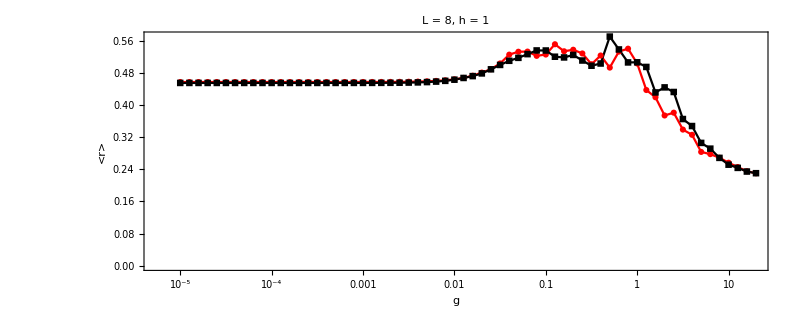

```mathematica
ListLogLinearPlot[{Transpose[{glist,data[[All,1]][[All,2]]}],Transpose[{glist,data[[All,2]][[All,2]]}]},PlotRange->All,PlotStyle->{Red,Black},PlotTheme->"Detailed",FrameLabel->{Style["g",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4,PlotLabel->Style["L = "<>ToString[L]<>", h = 1",25,Black]]
```

```mathematica
data=Import["/Users/pcs/Desktop/Entropy/EMMY r ratios Ising/r_L_8_g_1_log_h.m"];
```

Min::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

Min::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

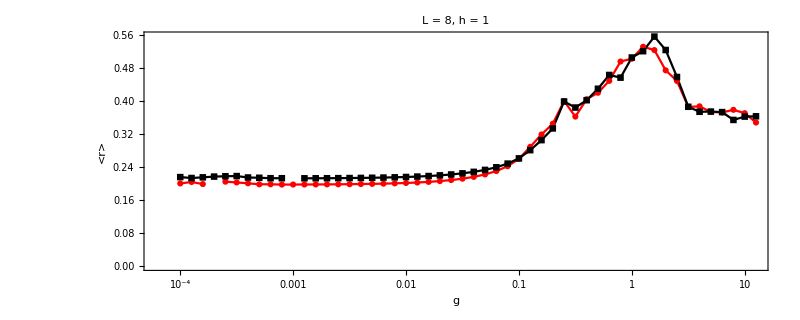

```mathematica
ListLogLinearPlot[{Transpose[{hlist,data[[All,1]][[All,2]]}],Transpose[{hlist,data[[All,2]][[All,2]]}]},PlotRange->All,PlotStyle->{Red,Black},PlotTheme->"Detailed",FrameLabel->{Style["g",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4,PlotLabel->Style["L = "<>ToString[L]<>", h = 1",25,Black]]
```

```mathematica
alldata=Import["/Users/pcs/Desktop/Entropy/schmidt modes/r_CLOSED_L_8_g_1_log_h.m"];
```

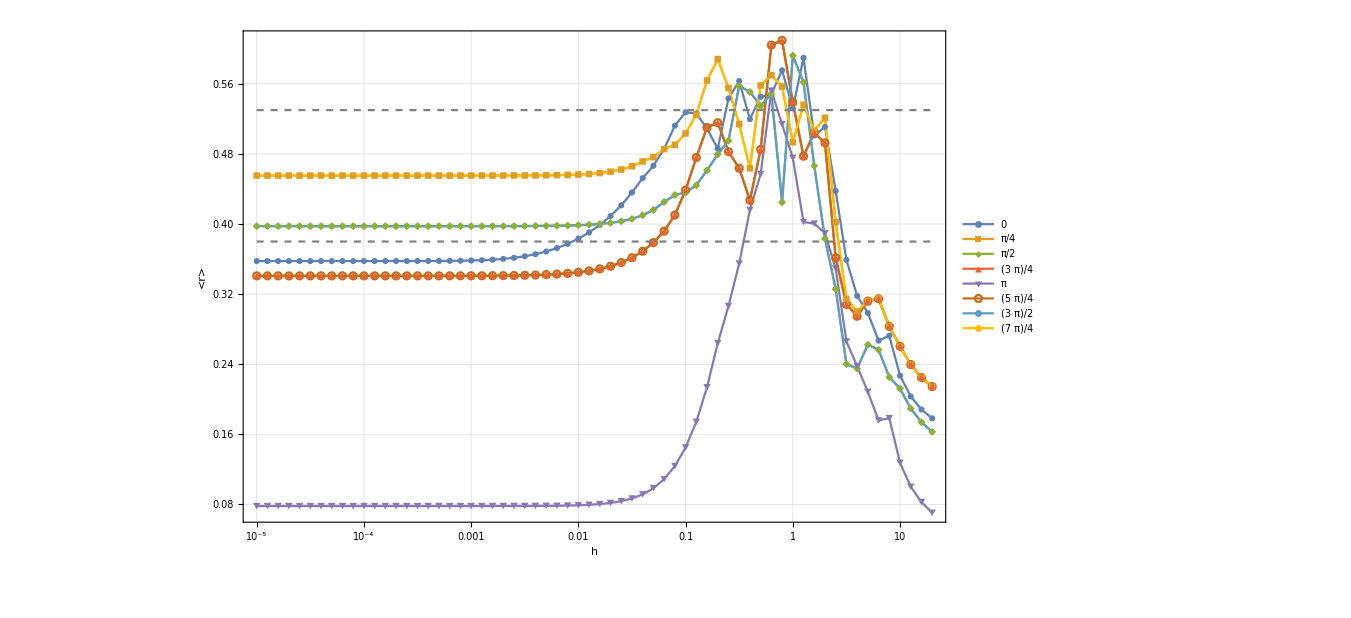

```mathematica
limits=LogLinearPlot[{0.38,0.53},{x,glist[[1]],glist[[-1]]},PlotStyle->Directive[Gray,Dashed]];
Show[ListLogLinearPlot[Transpose[alldata],Joined->True,PlotMarkers->Automatic,PlotTheme->"Detailed",FrameLabel->{Style["h",20,Black],Style["<r>",Black,20]},FrameStyle->Directive[Black,20],PlotLegends->Transpose[{{klist,ratios[[All,1]]}}]],limits,PlotRange->All,ImageSize->1000]
```

```mathematica
alldata=Import["/Users/pcs/Desktop/Entropy/schmidt modes/r_CLOSED_L_8_h_1_log_g.m"];
```

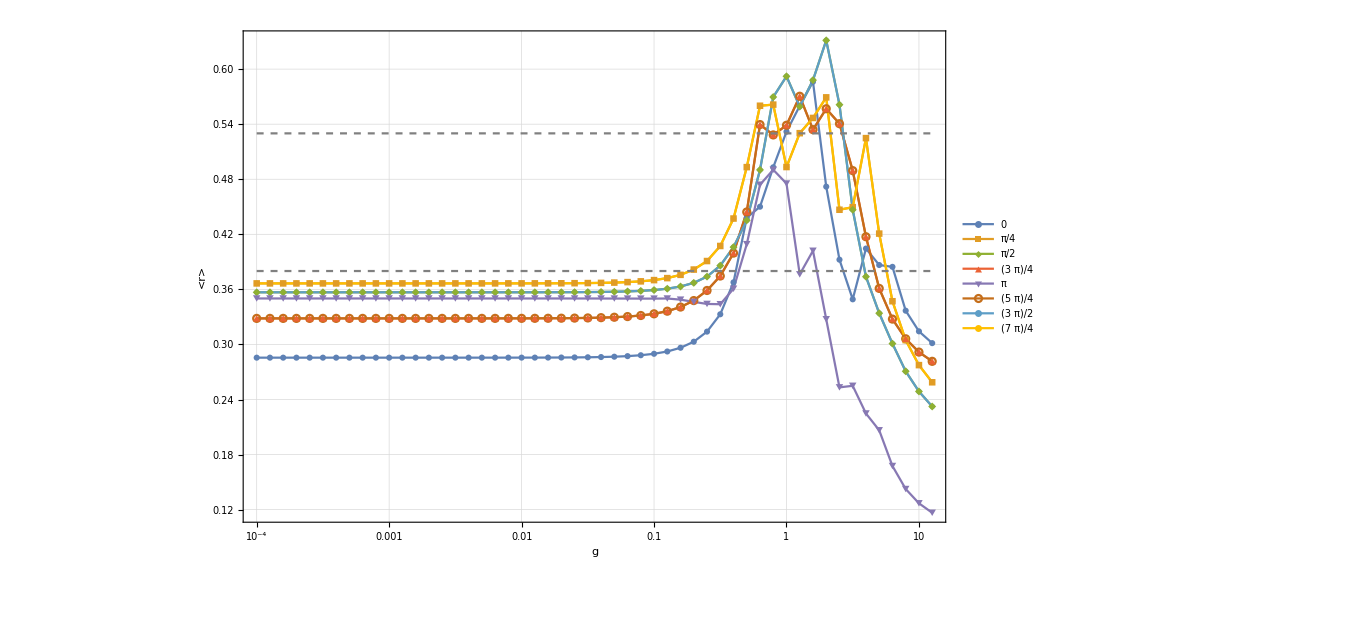

```mathematica
limits=LogLinearPlot[{0.38,0.53},{x,hlist[[1]],hlist[[-1]]},PlotStyle->Directive[Gray,Dashed]];
Show[ListLogLinearPlot[Transpose[alldata],Joined->True,PlotMarkers->Automatic,PlotTheme->"Detailed",FrameLabel->{Style["g",20,Black],Style["<r>",Black,20]},FrameStyle->Directive[Black,20],PlotLegends->Transpose[{{klist,ratios[[All,1]]}}],PlotRange->All],limits,PlotRange->All,ImageSize->1000]
```

# old mathematica

## original code

```mathematica
L=8;
basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];
```

```mathematica
J=1;
g=0.001;
h=1;
H=IsingNNOpenHamiltonian[h,g,J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
```

## new code

```mathematica
ClearAll[n];
Clear[opOnSite,reflectionOp];
opOnSite[op_,k_,n_]:=KroneckerProduct@@Table[If[i==k,op,id],{i,1,n}];
(*reflection operator*)
reflectionOp[n_]:=Module[{dim,perm,rules},dim=2^n;
perm=Table[FromDigits[Reverse[IntegerDigits[k,2,n]],2]+1,{k,0,dim-1}];
rules=Table[{i,perm[[i]]}->1,{i,dim}];
SparseArray[rules,{dim,dim}]]
```

```mathematica
n=L;
```

```mathematica
r=reflectionOp[n];
```

```mathematica
pplus=1/2 (IdentityMatrix[2^n]+r);
pminus=1/2 (IdentityMatrix[2^n]-r);
```

```mathematica
hplus=pplus.H.pplus;
hminus=pminus.H.pminus;
```

```mathematica
evenval=Eigenvalues[hplus];
oddval=Eigenvalues[hminus];
```

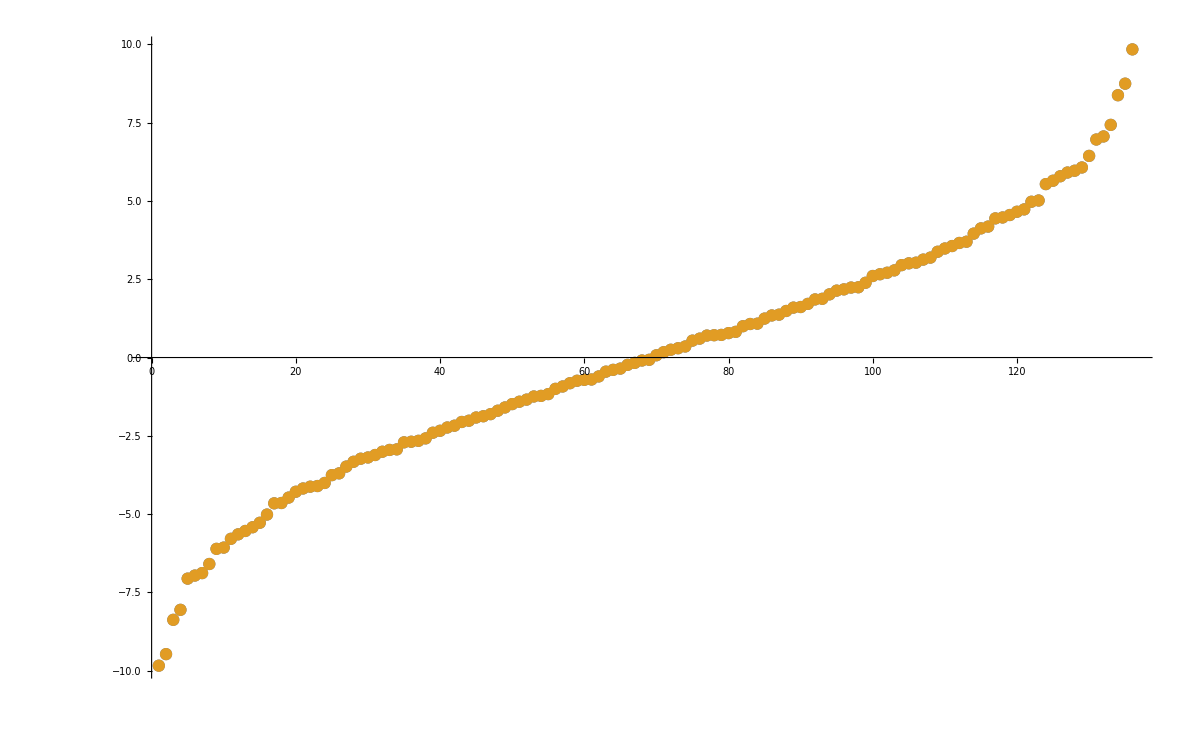

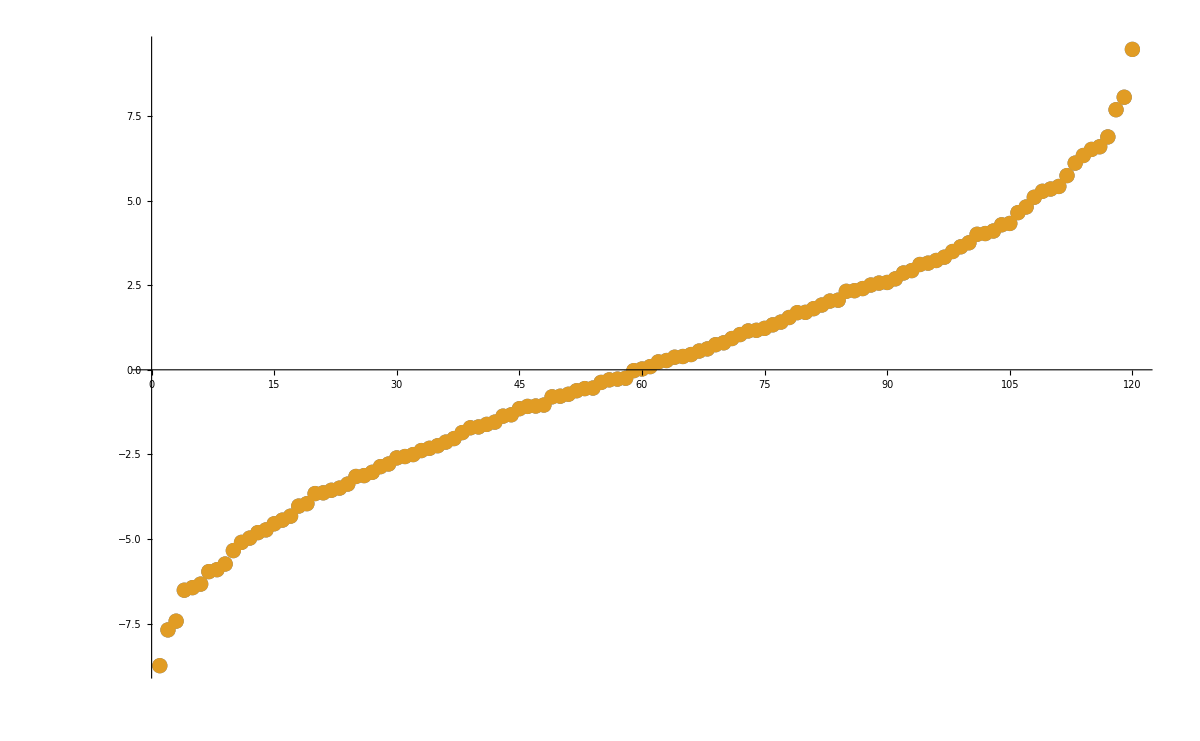

```mathematica
ListPlot[{Sort[eveneigenval],DeleteCases[Chop[Sort[evenval]],0]},PlotRange->All,ImageSize->1200]
ListPlot[{Sort[oddeigenval],DeleteCases[Chop[Sort[oddval]],0]},PlotRange->All,ImageSize->1200]
```

```mathematica
J=1;
glist=Table[10^i,{i,-5,1.3,0.1}];
newglist=Partition[glist,4];
hlist=Table[10^i,{i,-4,1.1,0.1}];
newhlist=Partition[hlist,4];
```